# A Dice Game

Each player

```mathematica
(* Num = Number of experiments per trial.*)
Num = 500;
Trials = 12;
(* Total number of experiments. *)
NN = Trials*Num;
SeedRandom[104]
```

```mathematica
PlayerNumber = 5;
```

```mathematica
(* Probabilities that each player rolls for the die.*)
```

```mathematica
PlayerProbs = {};
```

```mathematica
Do[PlayerProbs =Append[PlayerProbs,RandomInteger[{2,6}]/6],{PlayerNumber}]
PlayerProbs[[1]] = 1/3;
PlayerProbs[[2]]= 5/6;
```

```mathematica
(* List of the predictions cast by each player.*)
(* PlayerProbs *)
```

```mathematica
PlayerProbs = {1/3,5/6,2/3,1/6,1/2}
```

{1/3,5/6,2/3,1/6,1/2}

```mathematica
(* The actual die's probability for 'yes'*)
CorrectProb = PlayerProbs[[1]];
```

```mathematica
(* List of the predictions cast by each player.*)
probs = N[PlayerProbs]
```

{0.333333,0.833333,0.666667,0.166667,0.5}

```mathematica
probs
```

{0.333333,0.833333,0.666667,0.166667,0.5}

```mathematica
(* The probability that each player flips the a resolution to match their expectation.*)
ProbEA = 0.0;
ProbEB = 0.0;
```

```mathematica
PlayerError = {};
Do[PlayerError =Append[PlayerError,RandomReal[{0,1}]],{PlayerNumber}]
```

```mathematica
PlayerError
DefaultError = 0.0
PlayerError = {DefaultError,DefaultError,DefaultError,DefaultError,DefaultError,DefaultError}
```

{0.452133,0.916354,0.0191334,0.146677,0.758989}

0.

{0.,0.,0.,0.,0.,0.}

```mathematica
(* Randomly choose whether the experiment is true (1) or false (0)*)
ExperimentalResults = {};
num = 0;
For[i = 1,i≤ NN,i++,num =Random[Real,{0,1}];If[num≤ CorrectProb,ExperimentalResults =Append[ExperimentalResults,1],ExperimentalResults =Append[ExperimentalResults,-1]]]
(* Do[ExperimentalResults = Append[ExperimentalResults,2(Random[Integer,{0,1}]-1/2)],{i,NN}] *)
```

```mathematica
ExperimentalResults;
```

```mathematica
Yeses = Count[ExperimentalResults,1];
Noes = Count[ExperimentalResults,-1];
N[Yeses/NN]
N[Noes/NN]
```

0.331167

0.668833

```mathematica
Resolutions = {};
```

```mathematica
Do[Resolutions = Append[Resolutions,ExperimentalResults],{i,PlayerNumber}]
```

```mathematica
(* Modify each player's resolutions so that some are flipped in accordance with their E ratios.*)
Do[num = 0;For[i = 1,i≤ NN,i++,num =Random[Real,{0,1}];If[num ≤ PlayerError[[j]] && Resolutions[[j]][[i]]>0 && PlayerProbs[[j]] ≤ 0.5,Resolutions[[j]][[i]] = -Resolutions[[j]][[i]],Resolutions[[j]][[i]] = Resolutions[[j]][[i]]]],{j,PlayerNumber}]
Do[num = 0;For[i = 1,i≤ NN,i++,num =Random[Real,{0,1}];If[num ≤ PlayerError[[j]] && Resolutions[[j]][[i]]<0 && PlayerProbs[[j]] > 0.5,Resolutions[[j]][[i]] = -Resolutions[[j]][[i]],Resolutions[[j]][[i]] = Resolutions[[j]][[i]]]],{j,PlayerNumber}]
```

```mathematica
Predictions = {};
```

```mathematica
Do[Predictions = Append[Predictions,PlayerProbs[[i]]*(Range[NN]^0)],{i,PlayerNumber}]
```

```mathematica
(* A function to calculate the mean of all resolution lists. *)
ResolutionsMean[reses_,playercount_]:= Total[reses]/playercount
```

```mathematica
(* A list where each entry in the mean of the resolutions of all the players.*)
Avres =ResolutionsMean[Resolutions,PlayerNumber];
```

```mathematica
(* A function for calculating the outcomes (q in the draft) given a list of mean resolutions.*)
(* result is a placeholder list.*)
Outcome[avres_,result_]:=  (out = result;For[i = 1,i≤ NN,i++,Which[avres[[i]]> 0,out =Append[out,1],avres[[i]]< 0,out =Append[out,-1],avres[[i]]== 0,out =Append[out,0]]]; Return[out];);
```

```mathematica
(* blank is an empty list to use as a place holder. *)
blank = {};
(* a listof all the outcomes.*)
outcome =Outcome[Avres,blank];
```

```mathematica
Avres;
outcome;
```

```mathematica
(* A function for generating a list of suprisals given a list of probabilities (pros) for one player and a list of outcomes (outs)*)
Surprisals[pros_,outs_,result_]:= (surps = result;For[i = 1,i≤ NN,i++,Which[outs[[i]]==1,surps =Append[surps,-Log[pros]],outs[[i]]==  -1,surps =Append[surps,-Log[(1-pros)]],outs[[i]]==  0,surps =Append[surps,0]]]; Return[surps];);
```

```mathematica
(* Make a list of the lists of surprisals. *)
blank = {};
allsurprisals = {};
Do[allsurprisals = Append[allsurprisals,Surprisals[N[PlayerProbs[[j]]],outcome,blank]],{j,PlayerNumber}]
```

```mathematica
allsurprisals;
```

```mathematica
(* A function to generate a list of the means of the two players' surprisals, given a list of surprisal lists (surplist)*)
meansurps[surplist_,result_]:= (meansurs = result;For[i = 1,i≤ NN,i++,meansurs = Append[meansurs,Sum[surplist[[j]][[i]],{j,PlayerNumber}]/PlayerNumber ]]; Return[meansurs];);
```

```mathematica
(* A function to generate a list of the means of the two players' surprisals squared, given a list of surprisal lists (surplist)*)
meansurpsSqrd[surplist_,result_]:= (meansurssq = result;For[i = 1,i≤ NN,i++,meansurssq = Append[meansurssq, Sum[surplist[[j]][[i]]^2,{j,PlayerNumber}]/PlayerNumber ]]; Return[meansurssq];);
```

```mathematica
(* Make the actual lists of the means surprisals and the mean surprisals squared. *)
meansurprisals =meansurps[allsurprisals,blank];
meansurprisalsSqrd =meansurpsSqrd[allsurprisals,blank];
```

```mathematica
meansurprisals^2;
meansurprisalsSqrd;
```

```mathematica
(* Make a list of the spreads Δs *)
Spreads = Sqrt[meansurprisalsSqrd-meansurprisals^2];
(* Make a listof the s^Big *)
BigSurprises = meansurprisals+Spreads;
```

```mathematica
(* A function to generate a list of the rewards for a player given their surprisals (sur) the big surprisals (bigs) their resolutions (reses) and the spreads.*) 
rewards[surs_,bigs_,reses_,spreads_]:= Abs[reses]*Spreads*(bigs - surs)
```

```mathematica
(* Make a list of lists for each player's reward on each question. *)
Rewards = {};
Do[Rewards = Append[Rewards,rewards[allsurprisals[[j]],BigSurprises,Avres,Spreads]],{j,PlayerNumber}]
```

```mathematica
Rewards;
```

```mathematica
SumOfRewards = Total[Rewards];
```

```mathematica
(* A function to produce a list from lista where each entry is the sum of all previous entries in lista.*)
TotalSum[lista_,result_]:= (thesum = result;For[i = 1,i≤ NN,i++,thesum = Append[thesum,Total[lista[[1;;i]]]]]; Return[thesum];);
```

```mathematica
TotalSumNum[lista_,result_]:= (thesum = result;Do[For[i = 1,i≤ Num,i++,thesum = Append[thesum,{i,Total[lista[[1 +Num*(j-1);;i+Num*(j-1)]]]}]],{j,1,Trials}]; Return[thesum];);
```

```mathematica
absolutetotal =TotalSumNum[SumOfRewards,blank];
```

```mathematica
totalawards = {};
totalawardsnum = {};
```

```mathematica
Do[totalawards = Append[totalawards, TotalSum[Rewards[[k]],blank]]; Print["Player ", k, " Finished \n"],{k,PlayerNumber}]
Do[totalawardsnum = Append[totalawardsnum, TotalSumNum[Rewards[[k]],blank]];Print["Player ", k, " Finished \n"],{k,PlayerNumber}]
absolutetotal =TotalSumNum[SumOfRewards,blank];
```

Player 1 Finished

Player 2 Finished

Player 3 Finished

Player 4 Finished

Player 5 Finished

Player 1 Finished

Player 2 Finished

Player 3 Finished

Player 4 Finished

Player 5 Finished

```mathematica
(* Do[totalrewardsAnum = Append[totalrewardsAnum,{i,totalrewardsA[[i+Trials*(j-1)]]}],{j,Trials}] *)
```

```mathematica
totalrewardsAnum = totalawardsnum[[1]];
totalrewardsBnum =totalawardsnum[[2]];
totalrewardsCnum =totalawardsnum[[3]];
totalrewardsDnum = totalawardsnum[[4]];
totalrewardsEnum =totalawardsnum[[5]];
```

```mathematica
PlayerAwards =ListPlot[{totalrewardsAnum ,totalrewardsBnum ,totalrewardsCnum,totalrewardsDnum ,totalrewardsEnum },PlotLegends->Placed[{"Player A","Player B","Player C","Player D","Player E"},{Scaled[{0,0.3}], {-0.2, 0.1}}],AxesLabel-> {"Question #","Award"},PlotRange-> {0,Num/2.2},LabelStyle-> {Large}];
TotAwards =ListPlot[{absolutetotal},AxesLabel-> {"Question #","Award"},PlotStyle-> Black,PlotLabel-> "Total Award, All Players"];
```

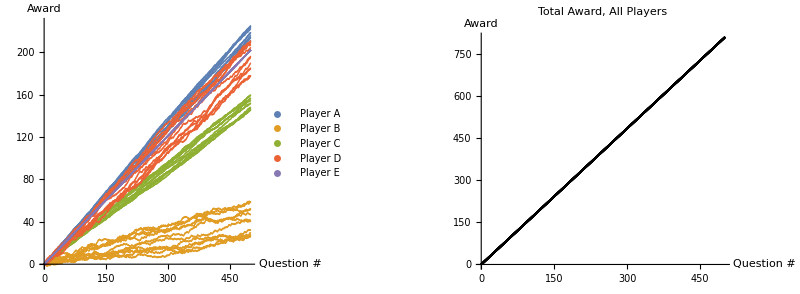

```mathematica
GraphicsRow[{PlayerAwards,TotAwards},Spacings->Scaled[0.3],PlotRangePadding->{0,{0,25}}]
```

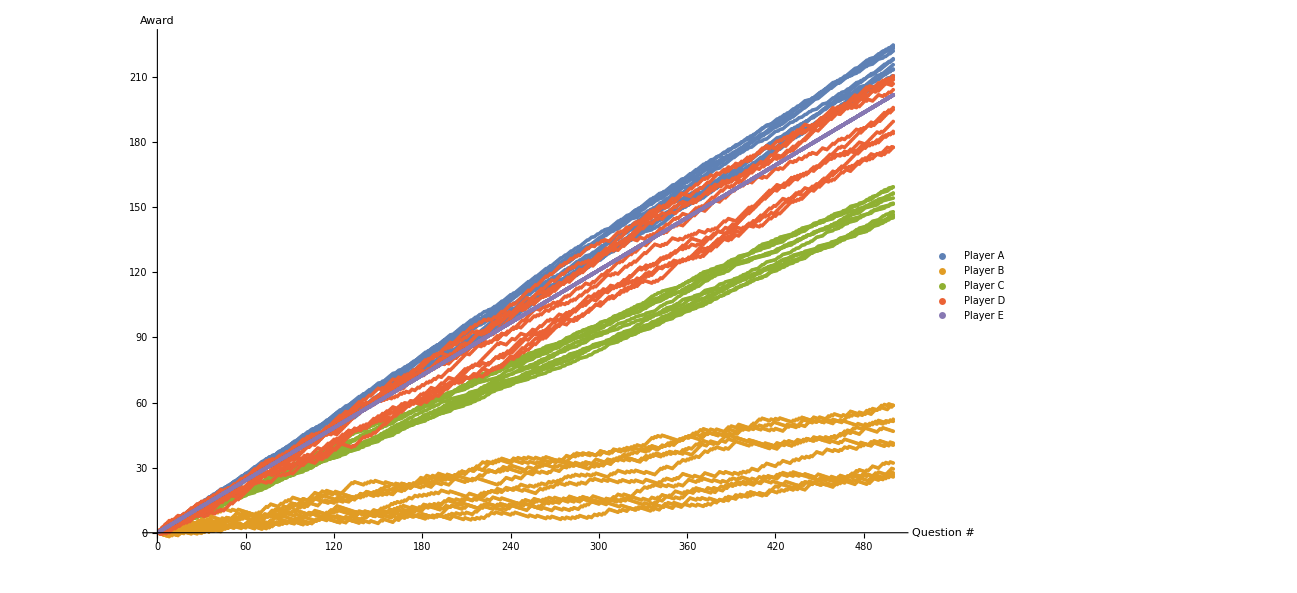

```mathematica
PlayerAwards
```

```mathematica
(* A function to calculate the mean of all entries in lista up to the kth entry. *)
TotalMeanNum[lista_,result_]:= (thesum = result;Do[For[i = 1,i≤ Num,i++,thesum = Append[thesum,{i,Total[lista[[1 +Num*(j-1);;i+Num*(j-1)]]]/i}]],{j,1,Trials}]; Return[thesum];);
```

```mathematica
(* A list of the mean surprisals up to the ith question for each separate player.*)
CumulativeSurprisals = {};
Do[CumulativeSurprisals = Append[CumulativeSurprisals,TotalMeanNum[allsurprisals[[k]],blank]],{k,PlayerNumber}]
```

```mathematica
CumulativeSurprisalA = CumulativeSurprisals[[1]];
CumulativeSurprisalB =CumulativeSurprisals[[2]];
CumulativeSurprisalC=CumulativeSurprisals[[3]];
CumulativeSurprisalD = CumulativeSurprisals[[4]];
CumulativeSurprisalE =CumulativeSurprisals[[5]];
```

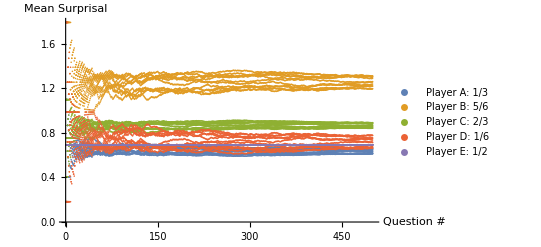

```mathematica
ListPlot[{CumulativeSurprisalA,CumulativeSurprisalB ,CumulativeSurprisalC,CumulativeSurprisalD ,CumulativeSurprisalE },PlotLegends->Placed[{StringForm["Player A: `1`",PlayerProbs[[1]]],StringForm["Player B: `1`",PlayerProbs[[2]]],StringForm["Player C: `1`",PlayerProbs[[3]]],StringForm["Player D: `1`",PlayerProbs[[4]]],StringForm["Player E: `1`",PlayerProbs[[5]]]},Above],AxesLabel-> {"Question #","Mean Surprisal"},LabelStyle-> {Large}]
```

```mathematica
(* Plot of the mean of the mean resolutions. *)
ResPlot =ListPlot[TotalMeanNum[Avres,blank],AxesLabel-> {"Question #","Mean Resolution"}];
(* Plot of the mean of the consensus. *)
ConsPlot =ListPlot[TotalMeanNum[Abs[Avres],blank],PlotRange-> {0,1.1},PlotStyle-> {Black},PlotLabel-> "Consensus"];
```

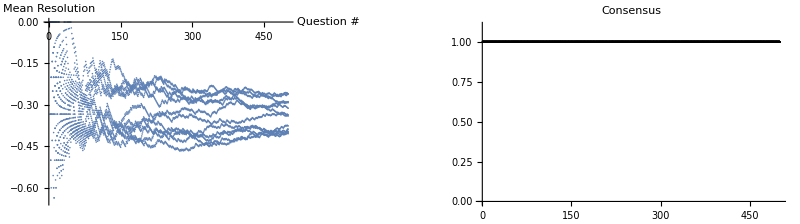

```mathematica
GraphicsRow[{ResPlot,ConsPlot},Spacings->Scaled[0.3],PlotRangePadding->{0,{0,25}}]
```